```mathematica
Max[2,3]
```

3

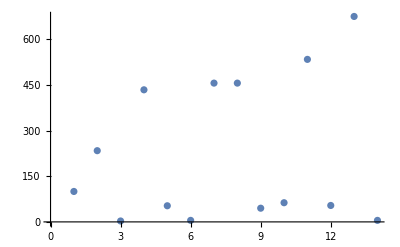

```mathematica
ListPlot[{100,234,3,434,53,5,456,456,45,63,534,54,675,5}]
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

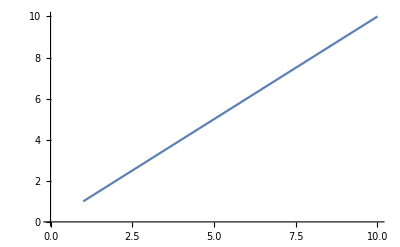

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

```mathematica
ListLinePlot[Range[10]]
```

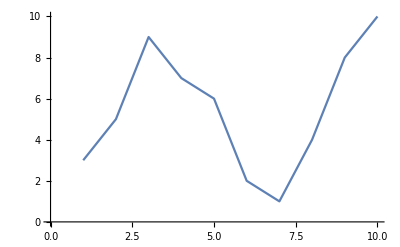

```mathematica
ListLinePlot[RandomSample[{1,2,3,4,5,6,7,8,9,10}]]
```

```mathematica
data1 = {#, #+RandomInteger[10], #*RandomReal[{1.8,2.3}]}&  /@ RandomSample[Range[30]]
```

{{23,30,48.3047},{7,8,14.6778},{4,11,7.66186},{1,9,2.05294},{24,25,44.3791},{6,11,13.2471},{21,30,39.5477},{10,10,21.2554},{13,21,27.4976},{12,12,24.8366},{18,20,37.5231},{5,10,11.0813},{15,20,31.5366},{25,29,56.5242},{17,17,32.7765},{11,19,20.6859},{16,24,29.7947},{27,35,55.9347},{28,29,56.1138},{30,33,59.0736},{19,22,39.3149},{20,30,40.2535},{3,11,6.4309},{26,28,57.3906},{29,29,54.9424},{14,19,25.911},{2,12,4.09924},{9,11,20.0146},{8,9,16.3811},{22,28,47.1147}}

```mathematica
ListPointPlot3D[data1]
```

-Graphics3D-